## Parameters

```mathematica
L=3 ;
J=1;
```

## Preliminary Functions

```mathematica
DocInnerProd[A_,B_] := Module[{psi},psi=Conjugate[Flatten[A]] . Flatten[B]]
```

### Functions to take tensor products of local operators

```mathematica
(*Given a binary number occupation rep of spins, it gives the corresponding matrix by taking a tensor product along the chain*)
ChainOccRepTensorProduct[OccRep_, Spin_] := Module[{a}, 
a=IdentityMatrix[1];
Do[ If[OccRep[[i]]==0, a = KroneckerProduct[a,IdentityMatrix[Dimensions[Spin]]]];
If[OccRep[[i]]==1, a = KroneckerProduct[a, Spin]];
,{i, 1, Length[OccRep]}];
a]
```

```mathematica
(*Takes Tensor product along the chain, with operator at position Position, and identities everywhere else*)
ChainTensorProduct[Length_,Operator_,Position_]:=Module[{list,chain},
list=ConstantArray[IdentityMatrix[2],Length];list[[Position]]=Operator;
chain=Apply[KroneckerProduct,list]]
```

```mathematica
(*Takes Tensor product along the chain, with operators at position Position and Position +1, and identities everywhere else*)
ChainNeighbourTensorProduct[Length_,Operator1_,Operator2_,Position_]:=Module[{list,chain}, 
list=ConstantArray[IdentityMatrix[2],Length];
(*If pos it at end, put Op1 at the end, and Op2 first, else just put Op1 at pos, and Op2 at pos+1*)
If[Position==Length, list[[Position]]=Operator1;list[[1]]=Operator2,list[[Position]]=Operator1;list[[Position+1]]=Operator2;];
chain=Apply[KroneckerProduct,list]]
```

```mathematica
JordanWignerTensorProduct[Length_,StringOperator_,Operator_,Position_]:=Module[{list,chain},
list=Join[ConstantArray[StringOperator,Position-1],{Operator},ConstantArray[IdentityMatrix[2],Length-Position]];
chain=Apply[KroneckerProduct,list]]
```

### Initialization functions

```mathematica
(*For Ising Matrix. Given a binary number occupation rep of spins, it gives the corresponding matrix*)
SpinStateMatrix[OccRep_, Spin_] := Module[{a}, 
a=IdentityMatrix[1];
Do[ If[OccRep[[i]]==0, a = KroneckerProduct[a,IdentityMatrix[Dimensions[Spin]]]];
If[OccRep[[i]]==1, a = KroneckerProduct[a, Spin]];
,{i, 1, Length[OccRep]}];
a]
```

```mathematica
(*For Ising Matrix. Given Length, Interaction Spins, Number of Interaction Spins (k-local), And the Spins for 2 magnetic fields, it Generates the Matrix representation.*)
IsingSum[L_,IntSpin_,IntSpinNo_,BSpin1_,BSpin2_]:=Module[{IntPerms, IntPieces, IntPart, B1Part, B2Part, SingleSpinPerms, B1Pieces, B2Pieces},
IntPerms = Table[Join[ConstantArray[0,i-1],ConstantArray[1,IntSpinNo],ConstantArray[0,L-(i-1)-IntSpinNo]],{i,1,L-IntSpinNo+1}];
SingleSpinPerms=Table[Join[ConstantArray[0,i-1],ConstantArray[1,1],ConstantArray[0,L-(i-1)-1]],{i,1,L}];
If[IntSpin == 0, IntPart = IntSpin, IntPart =IntSpin,
IntPieces = Table[SpinStateMatrix[IntPerms[[i]], IntSpin],{i, 1, Length[IntPerms]}];
IntPart = Total[IntPieces]];
If[BSpin1 == 0, B1Part=BSpin1,B1Part=BSpin1,
B1Pieces=Table[SpinStateMatrix[SingleSpinPerms[[i]],BSpin1],{i,1,Length[SingleSpinPerms]}];
B1Part = Total[B1Pieces]];
If[BSpin2 == 0, B2Part = BSpin2,B2Part=BSpin2,
B2Pieces =Table[SpinStateMatrix[SingleSpinPerms[[j]],BSpin2],{j,1,Length[SingleSpinPerms]}];
B2Part = Total[B2Pieces]];
IntPart+B1Part+B2Part]
```

## Ising Chain

```mathematica
HIsingIntMode[n_]:=-J*ChainNeighbourTensorProduct[L,PauliMatrix[3],PauliMatrix[3],n];
HIsingBMode[n_]:=-J*ChainTensorProduct[L,PauliMatrix[1],n];
```

```mathematica
HIsing = Sum[HIsingIntMode[n],{n,1,L-1}]+Sum[HIsingBMode[n],{n,1,L}];
HIsingNormed = HIsing/Sqrt[DocInnerProd[HIsing,HIsing]];
```

### Operators

```mathematica
σPlus0={{0,1},{0,0}};
σMinus0={{0,0},{1,0}};
```

```mathematica
σzMode[n_] := ChainTensorProduct[L, PauliMatrix[3], n];
σyMode[n_] := ChainTensorProduct[L, PauliMatrix[2], n];
σxMode[n_] := ChainTensorProduct[L, PauliMatrix[1], n];
σPlusMode[n_] := ChainTensorProduct[L, σPlus0, n];
σMinusMode[n_] := ChainTensorProduct[L, σMinus0, n];
```

```mathematica
σz = Sum[σzMode[n],{n,1,L}];
σy = Sum[σyMode[n],{n,1,L}];
σx = Sum[σxMode[n],{n,1,L}]; 
σPlus = Sum[σPlusMode[n],{n,1,L}]; 
σMinus = Sum[σMinusMode[n],{n,1,L}];
```

## The Kitaev Chain with 2x2 basis

CHECK IF THERE NEEDS TO BE AN AXIS PERMUTATION

### Operators

c_i= Π_(j<i)(σ^z)_j(σ^-)_i
(c^+)_i= Π_(j<i)(σ^z)_j(σ^+)_i

```mathematica
ccMode[n_]:=JordanWignerTensorProduct[L,PauliMatrix[3],σMinus0,n];
cdMode[n_]:=JordanWignerTensorProduct[L,PauliMatrix[3],σPlus0,n];
```

```mathematica
cc=Sum[ccMode[n],{n,1,L}];
cd = Sum[cdMode[n], {n, 1, L}];
```

## Return Amplitudes

### Brute Force

```mathematica
NormalizedReturnAmplitude[H_, Operator_]:=Module[{U,EvolvedOperator,NNNexpr,NNNnorm},
U=Refine[MatrixExp[-I*t*H],t ∈Reals];
EvolvedOperator=Refine[ConjugateTranspose[U].Operator.U ,t ∈Reals];
NNNexpr = FullSimplify[Expand[DocInnerProd[Operator,EvolvedOperator]],t ∈Reals];
NNNnorm = NNNexpr/.t->0;
NNNexpr=NNNexpr / NNNnorm]
```

```mathematica
NormalizedReturnAmplitude[HIsing,σx]
```

1/6 (1+4 Cos[2 t]+Cos[4 t])

### Diagonalizing the Hamiltonian

Eigensystem[H] returns a list where the first element is the Eigenvalues of H (EigVals), and the second is a matrix containing the Eigenvectors of H (EigVecs).  
H .Transpose[vecs]= Transpose[vecs].Diag[vals]
V.H.V^-1=D    and  V^-1.D.V= H

```mathematica
{vals,vecs} = Eigensystem[HIsing];
```

```mathematica
vals=N[vals,10];vecs=N[vecs,10];
```

```mathematica
U=Refine[Inverse[vecs].MatrixExp[I*t*DiagonalMatrix[vals]].vecs,t∈Reals];
```

```mathematica
Operator=σx;
```

```mathematica
EvolvedOperator=Refine[ConjugateTranspose[U].Operator.U,t∈Reals];
```

```mathematica
NNNexpr=FullSimplify[DocInnerProd[Operator,EvolvedOperator]];
NNNnorm = NNNexpr/.t->0;
NNNexpr=NNNexpr / NNNnorm
```

0.0416666667 (4.+16. Cos[2. t]+4. Cos[4. t]+0. Sin[2. t]+0. Sin[4. t])

```mathematica
ReturnAmplitudeByDiag[H_, Operator_,NPrec_]:=Module[{U,EvolvedOperator,NNNexpr,NNNnorm},
{vals,vecs} = Eigensystem[H];
vals=N[vals,NPrec];vecs=N[vecs,NPrec];
U=Refine[Inverse[vecs].MatrixExp[I*t*DiagonalMatrix[vals]].vecs,t∈Reals];
EvolvedOperator=Refine[ConjugateTranspose[U].Operator.U,t∈Reals];
NNNexpr=FullSimplify[DocInnerProd[Operator,EvolvedOperator]];
NNNnorm = NNNexpr/.t->0;
NNNexpr=NNNexpr / NNNnorm
]
```

```mathematica
ReturnAmplitudeByDiagChop[H_, Operator_,NPrec_]:=Module[{U,EvolvedOperator,NNNexpr,NNNnorm},
{vals,vecs} = Eigensystem[H];
vals=N[vals,NPrec];vecs=N[vecs,NPrec];
U=Refine[Inverse[vecs].MatrixExp[I*t*DiagonalMatrix[vals]].vecs,t∈Reals];
EvolvedOperator=Refine[ConjugateTranspose[U].Operator.U,t∈Reals];
NNNexpr=FullSimplify[Chop[DocInnerProd[Operator,EvolvedOperator], 10^-9]];
NNNnorm = NNNexpr/.t->0;
NNNexpr=NNNexpr / NNNnorm
]
```

```mathematica
ReturnAmplitudeByDiagChopChop[H_, Operator_,NPrec_]:=Module[{U,EvolvedOperator,NNNexpr,NNNnorm},
{vals,vecs} = Eigensystem[H];
vals=N[vals,NPrec];vecs=N[vecs,NPrec];
U=Refine[Inverse[vecs].MatrixExp[I*t*DiagonalMatrix[vals]].vecs,t∈Reals];
EvolvedOperator=Chop[Refine[ConjugateTranspose[U].Operator.U,t∈Reals],10^-9];
NNNexpr=FullSimplify[DocInnerProd[Operator,EvolvedOperator]];
NNNnorm = NNNexpr/.t->0;
NNNexpr=NNNexpr / NNNnorm
]
```

```mathematica
ReturnAmplitudeByDiagChopChopChop[H_, Operator_,NPrec_]:=Module[{U,EvolvedOperator,NNNexpr,NNNnorm},
{vals,vecs} = Eigensystem[H];
vals=N[vals,NPrec];vecs=N[vecs,NPrec];
U=Chop[Refine[Inverse[vecs].MatrixExp[I*t*DiagonalMatrix[vals]].vecs,t∈Reals], 10^-9];
EvolvedOperator=Refine[ConjugateTranspose[U].Operator.U,t∈Reals];
NNNexpr=FullSimplify[DocInnerProd[Operator,EvolvedOperator]];
NNNnorm = NNNexpr/.t->0;
NNNexpr=NNNexpr / NNNnorm
]
```

```mathematica
ReturnAmplitudeByDiagChoppy[H_, Operator_,NPrec_]:=Module[{U,EvolvedOperator,NNNexpr,NNNnorm},
{vals,vecs} = Eigensystem[H];
vals=N[vals,NPrec];vecs=N[vecs,NPrec];
U=Chop[Refine[Inverse[vecs].MatrixExp[I*t*DiagonalMatrix[vals]].vecs,t∈Reals],10^-9];
EvolvedOperator=ConjugateTranspose[U].Refine[Operator.U,t∈Reals];
NNNexpr=FullSimplify[Chop[DocInnerProd[Operator,EvolvedOperator],10^-9]];
NNNnorm = NNNexpr/.t->0;
NNNexpr=NNNexpr / NNNnorm
]
```

## Testing

```mathematica
ReturnAmplitudeByDiag[HIsing,σx,10];//Timing
ReturnAmplitudeByDiag[HIsing,σx,10];//Timing
ReturnAmplitudeByDiag[HIsing,σx,10];//Timing
```

{0.5,Null}

{0.453125,Null}

{0.421875,Null}

```mathematica
ReturnAmplitudeByDiagChop[HIsing, σx, 10];//Timing
ReturnAmplitudeByDiagChop[HIsing, σx, 10];//Timing
ReturnAmplitudeByDiagChop[HIsing, σx, 10];//Timing
```

{0.734375,Null}

{0.515625,Null}

{0.671875,Null}

```mathematica
ReturnAmplitudeByDiagChopChop[HIsing, σx, 10];//Timing
ReturnAmplitudeByDiagChopChop[HIsing, σx, 10];//Timing
ReturnAmplitudeByDiagChopChop[HIsing, σx, 10];//Timing
```

{0.59375,Null}

{0.78125,Null}

{0.71875,Null}

```mathematica
ReturnAmplitudeByDiagChopChopChop[HIsing, σx, 10];//Timing
ReturnAmplitudeByDiagChopChopChop[HIsing, σx, 10];//Timing
ReturnAmplitudeByDiagChopChopChop[HIsing, σx, 10];//Timing
```

{0.390625,Null}

{0.359375,Null}

{0.515625,Null}

```mathematica
ReturnAmplitudeByDiagChoppy[HIsing, σx, 10];//Timing
ReturnAmplitudeByDiagChoppy[HIsing, σx, 10];//Timing
ReturnAmplitudeByDiagChoppy[HIsing, σx, 10];//Timing
```

$Aborted

{106.234,Null}

{63.3906,Null}

```mathematica
NormalizedReturnAmplitude[HIsing,σx]//Timing
```

$Aborted

```mathematica
{vals,vecs} = Eigensystem[HIsing];//Timing
```

{4.70313,Null}

```mathematica
vals
```

{Root-4.76Root[-3-9 #1+3 #1^2+#1^3&,1]-4.758770483143634,Root4.76Root[3-9 #1-3 #1^2+#1^3&,3]4.758770483143634,Root-4.06Root[-19-9 #1+3 #1^2+#1^3&,1]-4.0641777724759125,Root4.06Root[19-9 #1-3 #1^2+#1^3&,3]4.0641777724759125,Root2.76Root[-19-9 #1+3 #1^2+#1^3&,3]2.7587704831436337,Root-2.76Root[19-9 #1-3 #1^2+#1^3&,1]-2.7587704831436337,Root-2.06Root[3-9 #1-3 #1^2+#1^3&,1]-2.064177772475912,Root2.06Root[-3-9 #1+3 #1^2+#1^3&,3]2.064177772475912,Root-1.69Root[-19-9 #1+3 #1^2+#1^3&,2]-1.6945927106677214,Root1.69Root[19-9 #1-3 #1^2+#1^3&,2]1.6945927106677214,-1,-1,1,1,Root-0.305Root[-3-9 #1+3 #1^2+#1^3&,2]-0.3054072893322786,Root0.305Root[3-9 #1-3 #1^2+#1^3&,2]0.3054072893322786}

## Testing station

```mathematica
FasterReturnAmp[H_,Operator_,NPrec_, ChopTol_]:=Module[{U,EvolvedOperator,NNNexpr,NNNnorm},
{vals,vecs} = Eigensystem[H];
vals=N[vals,NPrec];vecs=N[vecs,NPrec];
U=Chop[Refine[Inverse[vecs].MatrixExp[I*t*DiagonalMatrix[vals]].vecs,t∈Reals],ChopTol];
EvolvedOperator=ConjugateTranspose[U].Refine[Operator.U,t∈Reals];
NNNexpr=FullSimplify[Chop[DocInnerProd[Operator,EvolvedOperator],ChopTol], Assumptions->{t∈Reals}];
NNNnorm = NNNexpr/.t->0;
NNNexpr=NNNexpr / NNNnorm]
```

```mathematica
FasterReturnAmp[HIsing,σy,50, 10^-8]
```

0.125 (2.2111456180001682428726610650149790116475 Cos[1.2360679774997896964091736687312762354406183596 t]+5.7888543819998317571273389349850209883525 Cos[3.2360679774997896964091736687312762354406183596 t]+0. ⅈ Sin[1.2360679774997896964091736687312762354406183596 t]+0. ⅈ Sin[3.2360679774997896964091736687312762354406183596 t])

## Timing parts of the functions

```mathematica
$Assumptions=t∈Reals
```

t∈ℝ

```mathematica
H=HIsing;Operator=σx;
```

```mathematica
{vals,vecs} = Eigensystem[H];//Timing
```

{0.046875,Null}

```mathematica
vecs//MatrixForm//N
```

(1. | 0.554958 | 0.384043 | 0.554958 | 0.554958 | 0.384043 | 0.554958 | 1.
-1. | 1.44504 | 2.60388 | -1.44504 | 1.44504 | -2.60388 | -1.44504 | 1.
-1. | -0.24698 | -0.109916 | 0.24698 | -0.24698 | 0.109916 | 0.24698 | 1.
1. | 2.24698 | -9.09783 | 2.24698 | 2.24698 | -9.09783 | 2.24698 | 1.
0. | -1. | 0. | -1. | 1. | 0. | 1. | 0.
0. | 1. | 0. | -1. | -1. | 0. | 1. | 0.
-1. | 2.80194 | -3.49396 | -2.80194 | 2.80194 | 3.49396 | -2.80194 | 1.
1. | -0.801938 | -0.286208 | -0.801938 | -0.801938 | -0.286208 | -0.801938 | 1.)

```mathematica
Inverse[vecs]
```

{1}
 |  |  |  |

```mathematica
U=Inverse[vecs].MatrixExp[I*t*DiagonalMatrix[vals]].vecs;//Timing
```

{0.046875,Null}

```mathematica
ConjugateTranspose[U].Refine[Operator.U,t∈ Reals];//Timing
```

{2.54688,Null}

```mathematica
EvolvedOperator=ConjugateTranspose[U].Refine[Operator.U,t∈Reals];//Timing
```

{1.4375,Null}

```mathematica
x=DocInnerProd[Operator,EvolvedOperator];//Timing
```

{0.546875,Null}

```mathematica
x
```

$Aborted[]

```mathematica
Refine[x,]
```

```mathematica
Normal
```

```mathematica
FullSimplify[x, Assumptions->{t∈Reals}]//Timing
```

{0.296875,{0.,17.1428571+0. Cos[0.219832528 t]+0. Cos[0.89008374 t]+0. Cos[1.10991626 t]+0. Cos[1.6038755 t]+0. Cos[2. t]+0. Cos[2.49395921 t]+0.1851558 Cos[2.71379174 t]+4.719912 Cos[3.38404294 t]+0. Cos[3.60387547 t]+0. Cos[4.49395921 t]+0. Cos[5.20775094 t]+1.952075 Cos[6.09783468 t]+0. Cos[6.98791841 t]+0. ⅈ Sin[0.219832528 t]+0. ⅈ Sin[0.89008374 t]+0. ⅈ Sin[1.10991626 t]+0. ⅈ Sin[1.6038755 t]+0. ⅈ Sin[2. t]+0. ⅈ Sin[2.49395921 t]+0. ⅈ Sin[2.71379174 t]+0. ⅈ Sin[3.38404294 t]+0. ⅈ Sin[3.60387547 t]+0. ⅈ Sin[4.49395921 t]+0. ⅈ Sin[5.20775094 t]+0. ⅈ Sin[6.09783468 t]+0. ⅈ Sin[6.98791841 t]}}

```mathematica
temp=Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\K-Complexity of Ising Chain\\output\\ReturnAmpL4TFIMsz.txt"]
```

0.0650766794384382363`3.88809942349687*E^((0.6108145786645572091`6.0948782047337895*I)*t - (0.6108145786645572091`6.060699034113709*I)*Re[t]) + 0.0896398750170817145`3.88809942349687*E^((-1.7587704831436335363`6.52470280134383*I)*t - (0.6108145786645572091`6.060699034113709*I)*Re[t]) + 0.0083610349558920096`3.88809942349687*E^((2.3695850618081907453`6.6844197268086365*I)*t - (0.6108145786645572091`6.060699034113709*I)*Re[t]) + 0.8648142482326273304`3.88809942349687*E^((-4.4533631938113549317`6.927069543356128*I)*t - (0.6108145786645572091`6.060699034113709*I)*Re[t]) + 0.0381885631157690282`3.88809942349687*E^((5.0641777724759121407`7.015451984456669*I)*t - (0.6108145786645572091`6.060699034113709*I)*Re[t]) + 0.0650766794384382332`3.88809942349687*E^((-0.6108145786645572091`6.0948782047337895*I)*t + (0.6108145786645572091`6.060699034113709*I)*Re[t]) + 0.0896398750170817118`6.356717990192581*E^((1.7587704831436335363`6.52470280134383*I)*t + (0.6108145786645572091`6.060699034113709*I)*Re[t]) + 0.0083610349558920082`3.88809942349687*E^((-2.3695850618081907453`6.6844197268086365*I)*t + (0.6108145786645572091`6.060699034113709*I)*Re[t]) + 0.8648142482326273432`6.356717990192581*E^((4.4533631938113549317`6.927069543356128*I)*t + (0.6108145786645572091`6.060699034113709*I)*Re[t]) + 0.0381885631157690087`3.88809942349687*E^((-5.0641777724759121407`7.015451984456669*I)*t + (0.6108145786645572091`6.060699034113709*I)*Re[t]) + 1.3490469390337028513`5.064190682552549*E^((-0.6945927106677213954`6.120837266624948*I)*t - (2.`6.574753562969721*I)*Re[t]) + 1.777777777777777771`3.8880994234968678*E^((1.9999999999999999999`6.608845559144572*I)*t - (2.`6.574753562969721*I)*Re[t]) + 0.8648142482326273165`5.064190682552551*E^((-3.0641777724759121409`6.764443664900142*I)*t - (2.`6.574753562969721*I)*Re[t]) + 0.0083610349558920124`3.88809942349687*E^((3.7587704831436335361`6.8820862111519645*I)*t - (2.`6.574753562969721*I)*Re[t]) + 1.349046939033702847`5.511619950178323*E^((0.6945927106677213954`6.120837266624948*I)*t + (2.`6.574753562969721*I)*Re[t]) + 1.7777777777777777757`3.8880994234968678*E^((-1.9999999999999999999`6.608845559144572*I)*t + (2.`6.574753562969721*I)*Re[t]) + 0.8648142482326273925`5.511619950178323*E^((3.0641777724759121409`6.764443664900142*I)*t + (2.`6.574753562969721*I)*Re[t]) + 0.0083610349558920107`3.88809942349687*E^((-3.7587704831436335361`6.8820862111519645*I)*t + (2.`6.574753562969721*I)*Re[t]) + 1.3490469390337028512`5.064190682552549*E^((0.6945927106677213954`6.120837266624948*I)*t - (3.3891854213354427908`6.803252716323268*I)*Re[t]) + 0.0381885631157690224`3.88809942349687*E^((-1.0641777724759121409`6.3076760640075396*I)*t - (3.3891854213354427908`6.803252716323268*I)*Re[t]) + 2.5231246228334464243`3.8880994234968678*E^((3.3891854213354427907`6.8387940571401975*I)*t - (3.3891854213354427908`6.803252716323268*I)*Re[t]) + 0.0896398750170817249`3.88809942349687*E^((5.7587704831436335361`7.070077193463727*I)*t - (3.3891854213354427908`6.803252716323268*I)*Re[t]) + 1.3490469390337028457`3.8880994234968678*E^((-0.6945927106677213954`6.120837266624948*I)*t + (3.3891854213354427908`6.803252716323268*I)*Re[t]) + 0.0381885631157690144`5.511619950178323*E^((1.0641777724759121409`6.3076760640075396*I)*t + (3.3891854213354427908`6.803252716323268*I)*Re[t]) + 2.5231246228334464217`3.8880994234968678*E^((-3.3891854213354427907`6.8387940571401975*I)*t + (3.3891854213354427908`6.803252716323268*I)*Re[t]) + 0.0896398750170817084`3.88809942349687*E^((-5.7587704831436335361`7.070077193463727*I)*t + (3.3891854213354427908`6.803252716323268*I)*Re[t]) + 0.0896398750170817165`3.88809942349687*E^((1.7587704831436335363`6.52470280134383*I)*t - (4.1283555449518242816`6.888633521726539*I)*Re[t]) + 0.0083610349558920106`5.064190682552551*E^((2.3695850618081907453`6.6844197268086365*I)*t - (4.1283555449518242816`6.888633521726539*I)*Re[t]) + 0.3166160063115936935`3.88809942349687*E^((-2.6945927106677213954`6.707898849994381*I)*t - (4.1283555449518242816`6.888633521726539*I)*Re[t]) + 0.1015148575295991981`5.064190682552551*E^((4.1283555449518242816`6.924475820354641*I)*t - (4.1283555449518242816`6.888633521726539*I)*Re[t]) + 1.3490469390337028757`3.8880994234968678*E^((6.822948255619545677`7.143863535900737*I)*t - (4.1283555449518242816`6.888633521726539*I)*Re[t]) + 0.0896398750170817123`3.88809942349687*E^((-1.7587704831436335363`6.52470280134383*I)*t + (4.1283555449518242816`6.888633521726539*I)*Re[t]) + 0.0083610349558920146`3.88809942349687*E^((-2.3695850618081907453`6.6844197268086365*I)*t + (4.1283555449518242816`6.888633521726539*I)*Re[t]) + 0.3166160063115937167`5.511619950178323*E^((2.6945927106677213954`6.707898849994381*I)*t + (4.1283555449518242816`6.888633521726539*I)*Re[t]) + 0.1015148575295991976`3.88809942349687*E^((-4.1283555449518242816`6.924475820354641*I)*t + (4.1283555449518242816`6.888633521726539*I)*Re[t]) + 1.3490469390337028296`5.064190682552549*E^((-6.822948255619545677`7.143863535900737*I)*t + (4.1283555449518242816`6.888633521726539*I)*Re[t]) + 0.038188563115769007`3.88809942349687*E^((1.0641777724759121409`6.3076760640075396*I)*t - (5.5175409662872670724`7.014036943284353*I)*Re[t]) + 0.3166160063115937022`5.064190682552551*E^((-1.3054072893322786047`6.3931517528334645*I)*t - (5.5175409662872670724`7.014036943284353*I)*Re[t]) + 0.0083610349558920128`3.88809942349687*E^((3.7587704831436335361`6.8820862111519645*I)*t - (5.5175409662872670724`7.014036943284353*I)*Re[t]) + 3.6368343956167452581`3.8880994234968678*E^((5.5175409662872670723`7.048012190746165*I)*t - (5.5175409662872670724`7.014036943284353*I)*Re[t]) + 0.0381885631157690135`3.88809942349687*E^((-1.0641777724759121409`6.3076760640075396*I)*t + (5.5175409662872670724`7.014036943284353*I)*Re[t]) + 0.31661600631159371`5.511619950178323*E^((1.3054072893322786047`6.3931517528334645*I)*t + (5.5175409662872670724`7.014036943284353*I)*Re[t]) + 0.0083610349558920151`3.88809942349687*E^((-3.7587704831436335361`6.8820862111519645*I)*t + (5.5175409662872670724`7.014036943284353*I)*Re[t]) + 3.6368343956167452535`3.8880994234968678*E^((-5.5175409662872670723`7.048012190746165*I)*t + (5.5175409662872670724`7.014036943284353*I)*Re[t]) + 0.3166160063115937108`3.88809942349687*E^((1.3054072893322786047`6.3931517528334645*I)*t - (8.1283555449518242816`7.181234103624232*I)*Re[t]) + 0.8648142482326273826`5.064190682552551*E^((3.0641777724759121409`6.764443664900142*I)*t - (8.1283555449518242816`7.181234103624232*I)*Re[t]) + 0.089639875017081709`3.88809942349687*E^((5.7587704831436335361`7.070077193463727*I)*t - (8.1283555449518242816`7.181234103624232*I)*Re[t]) + 2.728929870438697211`3.8880994234968678*E^((8.1283555449518242816`7.218701419496351*I)*t - (8.1283555449518242816`7.181234103624232*I)*Re[t]) + 0.3166160063115937112`3.88809942349687*E^((-1.3054072893322786047`6.3931517528334645*I)*t + (8.1283555449518242816`7.181234103624232*I)*Re[t]) + 0.8648142482326273367`5.064190682552551*E^((-3.0641777724759121409`6.764443664900142*I)*t + (8.1283555449518242816`7.181234103624232*I)*Re[t]) + 0.0896398750170817045`3.88809942349687*E^((-5.7587704831436335361`7.070077193463727*I)*t + (8.1283555449518242816`7.181234103624232*I)*Re[t]) + 2.728929870438697204`3.8880994234968678*E^((-8.1283555449518242816`7.218701419496351*I)*t + (8.1283555449518242816`7.181234103624232*I)*Re[t]) + E^((-11.8871260280954578177`6.711264183162727*I)*t + (9.5175409662872670724`7.315668082662658*I)*Re[t])*(10.5000751296986292312`3.813917959828941*E^((2.3695850618081907453`6.6844197268086365*I)*t) + 1.3490469390337028541`3.813917959828941*E^((5.0641777724759121407`7.015451984456669*I)*t) + 0.0381889427988017569`3.813917959828941*E^((6.822948255619545677`7.143863535900737*I)*t) + 0.8648142482326273608`3.813917959828941*E^((7.433762834284102886`6.43584402475253*I)*t) + 0.3166160063115937184`3.813917959828941*E^((9.1925333174277364222`6.528210710502899*I)*t)) + (0.3166160063115937323`4.109948173113224*E^((2.6945927106677213954`6.707898849994381*I)*t) + 0.8648142482326273536`4.109948173113224*E^((4.4533631938113549317`6.927069543356128*I)*t) + 0.0381885631157690168`4.109948173113224*E^((5.0641777724759121407`7.015451984456669*I)*t) + 1.3490469390337028425`4.109948173113224*E^((6.822948255619545677`7.143863535900737*I)*t) + 10.5000751296986292379`4.109948173113224*E^((9.5175409662872670724`7.287223482350975*I)*t) - 0.0000972723416734995`4.109948173113224*Cosh[(0``6.343712038105914*I)*t])/E^((9.5175409662872670724`7.315668082662658*I)*Re[t])

```mathematica
expr=ToExpression[temp]
```

0.0651 ⅇ^(0.610815 ⅈ t-0.610815 ⅈ Re[t])+0.0896 ⅇ^(-1.75877 ⅈ t-0.610815 ⅈ Re[t])+0.00836 ⅇ^(2.36959 ⅈ t-0.610815 ⅈ Re[t])+0.865 ⅇ^(-4.45336 ⅈ t-0.610815 ⅈ Re[t])+0.0382 ⅇ^(5.064178 ⅈ t-0.610815 ⅈ Re[t])+0.0651 ⅇ^(-0.610815 ⅈ t+0.610815 ⅈ Re[t])+0.0896399 ⅇ^(1.75877 ⅈ t+0.610815 ⅈ Re[t])+0.00836 ⅇ^(-2.36959 ⅈ t+0.610815 ⅈ Re[t])+0.864814 ⅇ^(4.45336 ⅈ t+0.610815 ⅈ Re[t])+0.0382 ⅇ^(-5.064178 ⅈ t+0.610815 ⅈ Re[t])+1.349 ⅇ^(-0.694593 ⅈ t-2. ⅈ Re[t])+1.78 ⅇ^(2. ⅈ t-2. ⅈ Re[t])+0.86481 ⅇ^(-3.06418 ⅈ t-2. ⅈ Re[t])+0.00836 ⅇ^(3.75877 ⅈ t-2. ⅈ Re[t])+1.349 ⅇ^(0.694593 ⅈ t+2. ⅈ Re[t])+1.78 ⅇ^(-2. ⅈ t+2. ⅈ Re[t])+0.86481 ⅇ^(3.06418 ⅈ t+2. ⅈ Re[t])+0.00836 ⅇ^(-3.75877 ⅈ t+2. ⅈ Re[t])+1.349 ⅇ^(0.694593 ⅈ t-3.38919 ⅈ Re[t])+0.0382 ⅇ^(-1.06418 ⅈ t-3.38919 ⅈ Re[t])+2.52 ⅇ^(3.38919 ⅈ t-3.38919 ⅈ Re[t])+0.0896 ⅇ^(5.75877 ⅈ t-3.38919 ⅈ Re[t])+1.35 ⅇ^(-0.694593 ⅈ t+3.38919 ⅈ Re[t])+0.038189 ⅇ^(1.06418 ⅈ t+3.38919 ⅈ Re[t])+2.52 ⅇ^(-3.38919 ⅈ t+3.38919 ⅈ Re[t])+0.0896 ⅇ^(-5.75877 ⅈ t+3.38919 ⅈ Re[t])+0.0896 ⅇ^(1.75877 ⅈ t-4.12836 ⅈ Re[t])+0.008361 ⅇ^(2.36959 ⅈ t-4.12836 ⅈ Re[t])+0.317 ⅇ^(-2.69459 ⅈ t-4.12836 ⅈ Re[t])+0.10151 ⅇ^(4.12836 ⅈ t-4.12836 ⅈ Re[t])+1.35 ⅇ^(6.822948 ⅈ t-4.12836 ⅈ Re[t])+0.0896 ⅇ^(-1.75877 ⅈ t+4.12836 ⅈ Re[t])+0.00836 ⅇ^(-2.36959 ⅈ t+4.12836 ⅈ Re[t])+0.31662 ⅇ^(2.69459 ⅈ t+4.12836 ⅈ Re[t])+0.102 ⅇ^(-4.12836 ⅈ t+4.12836 ⅈ Re[t])+1.349 ⅇ^(-6.822948 ⅈ t+4.12836 ⅈ Re[t])+0.0382 ⅇ^(1.06418 ⅈ t-5.517541 ⅈ Re[t])+0.31662 ⅇ^(-1.30541 ⅈ t-5.517541 ⅈ Re[t])+0.00836 ⅇ^(3.75877 ⅈ t-5.517541 ⅈ Re[t])+3.64 ⅇ^(5.517541 ⅈ t-5.517541 ⅈ Re[t])+0.0382 ⅇ^(-1.06418 ⅈ t+5.517541 ⅈ Re[t])+0.31662 ⅇ^(1.30541 ⅈ t+5.517541 ⅈ Re[t])+0.00836 ⅇ^(-3.75877 ⅈ t+5.517541 ⅈ Re[t])+3.64 ⅇ^(-5.517541 ⅈ t+5.517541 ⅈ Re[t])+0.317 ⅇ^(1.30541 ⅈ t-8.128356 ⅈ Re[t])+0.86481 ⅇ^(3.06418 ⅈ t-8.128356 ⅈ Re[t])+0.0896 ⅇ^(5.75877 ⅈ t-8.128356 ⅈ Re[t])+2.73 ⅇ^(8.128356 ⅈ t-8.128356 ⅈ Re[t])+0.317 ⅇ^(-1.30541 ⅈ t+8.128356 ⅈ Re[t])+0.86481 ⅇ^(-3.06418 ⅈ t+8.128356 ⅈ Re[t])+0.0896 ⅇ^(-5.75877 ⅈ t+8.128356 ⅈ Re[t])+2.73 ⅇ^(-8.128356 ⅈ t+8.128356 ⅈ Re[t])+ⅇ^(-11.8871 ⅈ t+9.517541 ⅈ Re[t]) (10.5 ⅇ^(2.36959 ⅈ t)+1.35 ⅇ^(5.064178 ⅈ t)+0.0382 ⅇ^(6.822948 ⅈ t)+0.865 ⅇ^(7.43376 ⅈ t)+0.317 ⅇ^(9.19253 ⅈ t))+ⅇ^(-9.517541 ⅈ Re[t]) (0.3166 ⅇ^(2.69459 ⅈ t)+0.8648 ⅇ^(4.45336 ⅈ t)+0.03819 ⅇ^(5.064178 ⅈ t)+1.349 ⅇ^(6.822948 ⅈ t)+10.5 ⅇ^(9.517541 ⅈ t)-0.00009727 Cosh[0. ⅈ t])

```mathematica
expr/.t->1
```

36.9+0. ⅈ

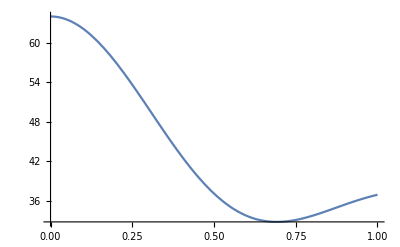

```mathematica
Plot[Re[expr],{t,0,1}]
```

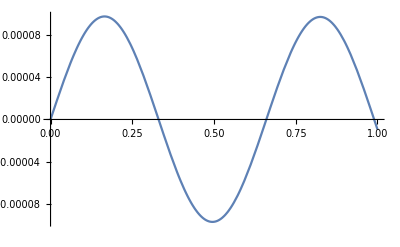

```mathematica
Plot[Im[expr],{t,0,1}]
```